This notebook is for plotting the data that is produced in micrOMEGAs. 

The data comes in as one seven part vector for each loop iteration. The seven parts of a single loop iteration are: 

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in 1000000%, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

```mathematica
file4=<<"/Users/ruppell/Math/temp/output.txt";
zaxel=Flatten@file4[[All,2,22]];
yaxel=Flatten@file4[[All,6,1]];
xaxel=Abs@file4[[All,3,5,1]];

data4omega=Transpose@{xaxel,yaxel};
data4omega3D=Transpose@{xaxel,zaxel,Log@yaxel};
num=First@Dimensions@file4/150+1;
```

```mathematica
Dimensions@file4
```

{2000,7}

```mathematica
channelSort={"e2 E2"->"dD","e3 E3"->"dD","n4 n4"->"N4 N4","c C"->"uU","s S"->"dD", "b B"->"dD"};
channelsLSP=Union@Flatten@file4[[All,5,All,4]];
channelsSNEU=Union@Flatten@file4[[All,7,All,3]];
percentsLSP=file4[[All,5,All,{4,1}]]/.List[s_,p_]/;(Head@s===String):>Rule[s,N[p]];
crosssecLSP=file4[[All,5,All,{4,2}]]/.List[s_,p_]/;(Head@s===String):>Rule[s,N[p]];
crosssecSNEU=Select[#,Head@#===Rule&]&/@(file4[[All,7,All]]/.List[p_,q_,r_]/;(Head@r===String&&q=="~n1 ~n1"):>Rule[r,N[p]]);
zero={k_/;Head@k===String->0};
decaysPercentLSP=Transpose@(channelsLSP/.percentsLSP/.zero);
decaysCrossecLSP=Transpose@(channelsLSP/.crosssecLSP/.zero);
decaysCrossecSNEU=Transpose@(channelsSNEU/.crosssecSNEU/.zero);

data4BRprcnLSP=Transpose@{xaxel,#}&/@decaysPercentLSP;
data4BRcrscLSP=Transpose@{xaxel,#}&/@decaysCrossecLSP;
data4BRcrscSNEU=Transpose@{xaxel,#}&/@decaysCrossecSNEU;
```

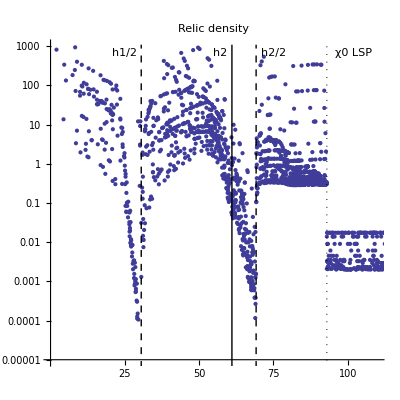

```mathematica
Show[
ListLogPlot[data4omega,
PlotRange->{{0,110},{10^-5,10^3}},
AspectRatio->1,
PlotLabel->"Relic density",
Ticks->{{{5,"",0.01},{10,"",0.01},{15,"",0.01},{20,"",0.01},25,
{30,"",0.01},{35,"",0.01},{40,"",0.01},{45,"",0.01},50,
{55,"",0.01},{60,"",0.01},{65,"",0.01},{70,"",0.01},75,
{80,"",0.01},{85,"",0.01},{90,"",0.01},{95,"",0.01},100,
{105,"",0.01},{110,"",0.01}},{1000,100,10,1,0.1,0.01,0.001,0.0001,0.00001}}],
Graphics[Line@{{file4[[1,3,6,2]],-12},{file4[[1,3,6,2]],7}}],
Graphics[{Dashed,Line@{{file4[[1,3,6,2]]/2,-12},{file4[[1,3,6,2]]/2,7}}}],
Graphics[{Dashed,Line@{{file4[[1,3,6,3]]/2,-12},{file4[[1,3,6,3]]/2,7}}}],
Graphics[{Dotted,Line@{{file4[[1,3,1,1]],-12},{file4[[1,3,1,1]],7}}}],
Graphics[Text["h1/2",{25,6.5}]],
Graphics[Text["h2",{57,6.5}]],
Graphics[Text["h2/2",{75,6.5}]],
Graphics[Text["χ0 LSP",{102,6.5}]]
]
```

```mathematica
Export["/Users/ruppell/Fig7b.eps",%148];
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
data4BRcrscSNEUsort={#[[1]],#[[5]],#[[6]],{#[[1]]/2,#[[2]]}&/@(#[[7]]+#[[8]]),#[[10]],#[[11]]}&@data4BRcrscSNEU;
channelsSNEUsort={"b B","h1 h1","h2 h2","N4 N4","W+ W-","Z Z"};
```

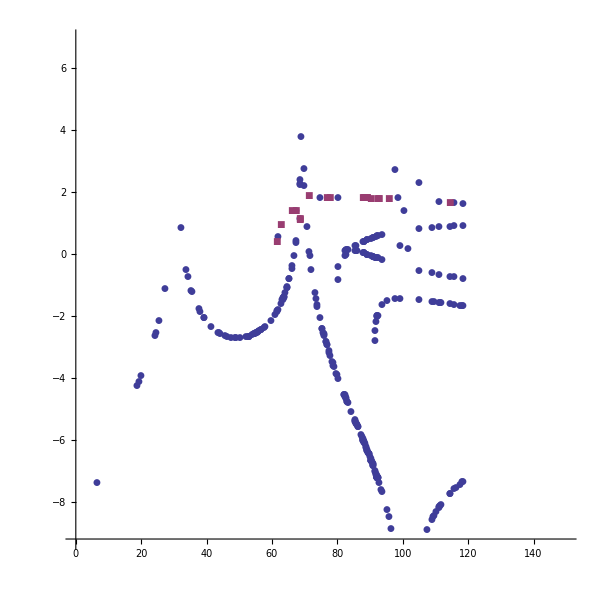

```mathematica
ListLogPlot[
data4BRcrscSNEUsort,
PlotRange->{{0,150},{0.0001,1000}},
ImageSize->{600,600},
AspectRatio->1,
PlotMarkers->Automatic,
PlotLegend->channelsSNEUsort,
LegendPosition->{1.1,-0.4}]
```